```mathematica
UserDirectory=ToFileName[("FileName"/.NotebookInformation[EvaluationNotebook[]])[[1]]];
SetDirectory[UserDirectory<>"_output"]
DataTransformation[x_String]:=ToExpression@StringReplace[x,"E"-> "*10^"]
ϵ=10 ^-4;(* tolérance *)
```

D:\AVAC\_output

```mathematica
listeQ=FileNames["fort.q*"]
listeT=FileNames["fort.t*"];
Length@listeQ
```

{fort.q0000,fort.q0001,fort.q0002,fort.q0003,fort.q0004,fort.q0005,fort.q0006,fort.q0007,fort.q0008,fort.q0009,fort.q0010,fort.q0011,fort.q0012,fort.q0013,fort.q0014,fort.q0015,fort.q0016,fort.q0017,fort.q0018,fort.q0019,fort.q0020,fort.q0021,fort.q0022,fort.q0023,fort.q0024,fort.q0025,fort.q0026,fort.q0027,fort.q0028,fort.q0029,fort.q0030,fort.q0031,fort.q0032,fort.q0033,fort.q0034,fort.q0035,fort.q0036,fort.q0037,fort.q0038,fort.q0039,fort.q0040,fort.q0041,fort.q0042,fort.q0043,fort.q0044,fort.q0045,fort.q0046,fort.q0047,fort.q0048,fort.q0049,fort.q0050,fort.q0051,fort.q0052,fort.q0053,fort.q0054,fort.q0055,fort.q0056,fort.q0057,fort.q0058,fort.q0059,fort.q0060,fort.q0061,fort.q0062,fort.q0063,fort.q0064,fort.q0065,fort.q0066,fort.q0067,fort.q0068,fort.q0069,fort.q0070,fort.q0071,fort.q0072,fort.q0073,fort.q0074,fort.q0075,fort.q0076,fort.q0077,fort.q0078,fort.q0079,fort.q0080,fort.q0081,fort.q0082,fort.q0083,fort.q0084,fort.q0085,fort.q0086,fort.q0087,fort.q0088,fort.q0089,fort.q0090,fort.q0091,fort.q0092,fort.q0093,fort.q0094,fort.q0095,fort.q0096,fort.q0097,fort.q0098,fort.q0099,fort.q0100}

101

```mathematica
Directory[]
```

D:\_output

## Topo Importation

```mathematica
TopoDirectory="D:/qgis_recoin2018";
SetDirectory[TopoDirectory]
NoDataValue=1400;
```

D:\qgis_recoin2018

210

{204,289}

{204,289}

6.451135×10^6

925720.

204

289

5.

5.

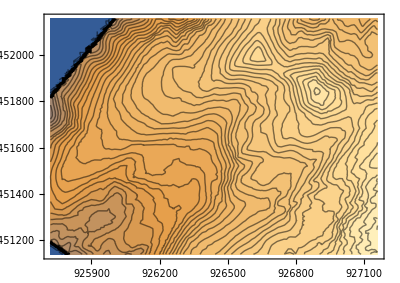

D:\_output

```mathematica
data=ReadList["topo5m.asc",String,RecordLists->True];
dim= Length@data

newdata=Replace[ndata,Except[_?NumericQ]->NoDataValue,{2}];
Dimensions@newdata
Dimensions@ndata

ymin=StringCases[data[[4,1]],x:NumberString:>ToExpression[x]][[1]]
xmin=StringCases[data[[3,1]],x:NumberString:>ToExpression[x]][[1]]
 ny=StringCases[data[[2,1]],x:NumberString:>ToExpression[x]][[1]]
 nx=StringCases[data[[1,1]],x:NumberString:>ToExpression[x]][[1]]
ndata={};
Do[AppendTo[ndata,Flatten@ToExpression@StringSplit[data[[i,1]]," "]],{i,7,dim}]
pasX=StringCases[data[[5,1]],x:NumberString:>ToExpression[x]][[1]]
pasY=StringCases[data[[5,1]],x:NumberString:>ToExpression[x]][[1]]

tableauTopo=Flatten[Table[{xmin+(i-1) pasX,ymin+(ny-k+1) pasX,newdata[[k,i]]},{i,nx},{k,ny}],1];
fnc=Interpolation[tableauTopo];
{{XTmin,XTmax},{YTmin,YTmax}}=ReleaseHold@Extract[fnc,1,Hold];
zTopoMin=Min[#[[3]]&/@tableauTopo];
zTopoMax=Max[#[[3]]&/@tableauTopo];
vue=ContourPlot[fnc[x,y],{x,XTmin,XTmax},{y,YTmin,YTmax},Contours->Range[zTopoMin,zTopoMax,10], AspectRatio->(YTmax-ymin)/(XTmax-xmin) ]
SetDirectory[UserDirectory]
```

## Reading a map

### Level One Reading

```mathematica
index=50;
dataTimes=ReadList[listeT[[index]],"Word",RecordLists->True];
infoTimes={#[[2]],DataTransformation[#[[1]] ]}&/@Take[dataTimes,3];
ttt=infoTimes[[1,2]];
Print["■ Computation made at time t = ",ttt];

data=ReadList[listeQ[[index]],"Word",RecordLists->True];
ngrid=Count[data,{"1","AMR_level"}];
ngrid2=Count[data,{"2","AMR_level"}];
ngrid3=Count[data,{"3","AMR_level"}];
If[index<10,indexName="0"<>ToString[index],indexName=ToString[index]];
nameFile="fort.q00"<>indexName;
nameFileTimes="fort.t00"<>indexName;
data=ReadList[listeQ[[index]],"Word",RecordLists->True];
values=Drop[data,8];
info={#[[2]],DataTransformation[#[[1]] ]}&/@Take[data,8];


If[ngrid==1,Print["● I have found only 1 grid."],Print["● There are ",ngrid," grids of level 1."]]
If[ngrid==1,
δx=info[[7,2]];
δy=info[[8,2]];
mx=info[[3,2]];
my=info[[4,2]];
xll=info[[5,2]];
yll=info[[6,2]];
yup=yll+my δy;(* coin gauche haut *)
col1=ArrayReshape[Table[DataTransformation@values[[k,1]],{k,mx my}],{my,mx}];(* my lignes de mx colonnes *)
col2=ArrayReshape[Table[DataTransformation@values[[k,2]],{k,mx my}],{my,mx}];
col3=ArrayReshape[Table[DataTransformation@values[[k,3]],{k,mx my}],{my,mx}];
col4=ArrayReshape[Table[DataTransformation@values[[k,4]],{k,mx my}],{my,mx}];
setH=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy ,col1[[i,j]]},{i,my},{j,mx} ];
setHUx=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy ,If[col1[[i,j]]>ϵ,col2[[i,j]]/col1[[i,j]],0]},{i,my},{j,mx} ];
setHUy=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy ,If[col1[[i,j]]>ϵ,col3[[i,j]]/col1[[i,j]],0]},{i,my},{j,mx} ];
setEta=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy  ,col4[[i,j]]},{i,my},{j,mx} ];
Print["Coordonnées du coin bas gauche : ",xll,", ",yll];
Print["Domaine de calcul en x : [",xll ,", ",xll+mx δx,"] avec un pas de δx = ",δx];
Print["Domaine de calcul en y : [",yll ,", ",yll+my δy,"] avec un pas de δy = ",δy];
dessinH=ListDensityPlot[ Flatten[setH,1],Frame->True ];
dessinUx=ListDensityPlot[ Flatten[setHUx,1],Frame->True ];
dessinUy=ListDensityPlot[ Flatten[setHUy,1],Frame->True ];
dessinEta=ListDensityPlot[ Flatten[setEta,1],Frame->True ];
interEta[index]=Interpolation[Flatten[setEta,1]];
interH[index]=Interpolation[Flatten[setH,1]];
{{xmin,xmax},{ymin,ymax}}=interEta[index]["Domain"]
]
 
 
If[ngrid>1,
igrid=1;start=0;
While[igrid<=ngrid,
info={#[[2]],DataTransformation[#[[1]] ]}&/@Take[data,{start+1,start+8}];
infogrid=info[[1,2]];
infolevel=info[[2,2]];
mx=info[[3,2]];
my=info[[4,2]];
xll=info[[5,2]];
yll=info[[6,2]];
δx=info[[7,2]];
δy=info[[8,2]];
Print["→ Reading grid ",igrid," with ",my, " lines × ",mx, " columns. ClawPack ref: ", infogrid, " (AMR level ",infolevel,")"];
yup=yll+my δy;(* coin gauche haut *)
values=Take[data,{start+9,start+8+mx my}];
col1=ArrayReshape[Table[DataTransformation@values[[k,1]],{k,mx my}],{my,mx}];(* my lignes de mx colonnes *)
col2=ArrayReshape[Table[DataTransformation@values[[k,2]],{k,mx my}],{my,mx}];
col3=ArrayReshape[Table[DataTransformation@values[[k,3]],{k,mx my}],{my,mx}];
col4=ArrayReshape[Table[DataTransformation@values[[k,4]],{k,mx my}],{my,mx}];
PartH[igrid]=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy ,col1[[i,j]]},{i,my},{j,mx} ];
PartHUx[igrid]=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy ,If[col1[[i,j]]>ϵ,col2[[i,j]]/col1[[i,j]],0]},{i,my},{j,mx} ];
PartHUy[igrid]=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy  ,If[col1[[i,j]]>ϵ,col3[[i,j]]/col1[[i,j]],0]},{i,my},{j,mx} ];
PartEta[igrid]=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy  ,col4[[i,j]]},{i,my},{j,mx} ];
PartPre[igrid]=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy  ,0.5*300(If[col1[[i,j]]>ϵ,col2[[i,j]]/col1[[i,j]],0]^2+If[col1[[i,j]]>ϵ,col3[[i,j]]/col1[[i,j]],0]^2)/1000},{i,my},{j,mx} ];
Print["  Grid ",igrid," whose left lower point is located at: (",xll,", ",yll,")"];
Print["  Grid ",igrid," – computational domaine, x range : [",xll ,", ",xll+mx δx,"] with a step δx = ",δx];
Print["  Grid ",igrid," – computational domaine, y range : [",yll ,", ",yll+my δy,"] with a step δy = ",δy];
dessinPartH[igrid]=ListDensityPlot[ Flatten[PartH[igrid],1],Frame->True ];
dessinPartHUx[igrid]=ListDensityPlot[ Flatten[PartHUx[igrid],1],Frame->True ];
dessinPartHUy[igrid]=ListDensityPlot[ Flatten[PartHUy[igrid],1],Frame->True ];
dessinPartEta[igrid]=ListDensityPlot[ Flatten[PartEta[igrid],1],Frame->True ];
dessinPartPre[igrid]=ListDensityPlot[ Flatten[PartPre[igrid],1],Frame->True ];
igrid+=1;
start+=mx my+8
 ];
interEta[index]=Interpolation[Flatten[ Table[PartEta[i],{i,ngrid}] ,2],InterpolationOrder->1];
interH[index]=Interpolation[Flatten[ Table[PartH[i],{i,ngrid}] ,2],InterpolationOrder->1];
interP[index]=Interpolation[Flatten[ Table[PartPre[i],{i,ngrid}] ,2],InterpolationOrder->1];
{{xmin,xmax},{ymin,ymax}}=interEta[index]["Domain"]
] 
If[ngrid2>0,Print["⟶ There are higher level grids. I see ",ngrid2," level-2 grids. Continue to proceed..."],"Done."]
```

■ Computation made at time t = 196.

● There are 4 grids of level 1.

→ Reading grid 1 with 50 lines × 50 columns. ClawPack ref: 4 (AMR level 1)

Grid 1 whose left lower point is located at: (926210., 6.45165×10^6)

Grid 1 – computational domaine, x range : [926210., 926700.] with a step δx = 9.8

Grid 1 – computational domaine, y range : [6.45165×10^6, 6.45216×10^6] with a step δy = 10.15

→ Reading grid 2 with 50 lines × 50 columns. ClawPack ref: 2 (AMR level 1)

Grid 2 whose left lower point is located at: (926210., 6.45114×10^6)

Grid 2 – computational domaine, x range : [926210., 926700.] with a step δx = 9.8

Grid 2 – computational domaine, y range : [6.45114×10^6, 6.45165×10^6] with a step δy = 10.15

→ Reading grid 3 with 50 lines × 50 columns. ClawPack ref: 3 (AMR level 1)

Grid 3 whose left lower point is located at: (925720., 6.45165×10^6)

Grid 3 – computational domaine, x range : [925720., 926210.] with a step δx = 9.8

Grid 3 – computational domaine, y range : [6.45165×10^6, 6.45216×10^6] with a step δy = 10.15

→ Reading grid 4 with 50 lines × 50 columns. ClawPack ref: 1 (AMR level 1)

Grid 4 whose left lower point is located at: (925720., 6.45114×10^6)

Grid 4 – computational domaine, x range : [925720., 926210.] with a step δx = 9.8

Grid 4 – computational domaine, y range : [6.45114×10^6, 6.45165×10^6] with a step δy = 10.15

{{925725.,926695.},{6.45115×10^6,6.45215×10^6}}

⟶ There are higher level grids. I see 2 level-2 grids. Continue to proceed...

### Level Two Reading (if AMRClaw is used)

```mathematica
If[
ngrid2>0,Print["Reading on... ",ngrid2, " grids."];
data2=Drop[data,start];
igrid=1;start=0;
While[igrid<=ngrid2,
info={#[[2]],DataTransformation[#[[1]] ]}&/@Take[data2,{start+1,start+8}];
infogrid=info[[1,2]];
infolevel=info[[2,2]];
mx=info[[3,2]];
my=info[[4,2]];
xll=info[[5,2]];
yll=info[[6,2]];
δx=info[[7,2]];
δy=info[[8,2]];
Print["→ I am reading ",igrid," of size ",my, " lines × ",mx, " columns. ClawPack ref: ", infogrid, " (AMR level ",infolevel,")"];
yup=yll+my δy;(* coin gauche haut *)
values=Take[data2,{start+9,start+8+mx my}];
col1=ArrayReshape[Table[DataTransformation@values[[k,1]],{k,mx my}],{my,mx}];(* my lignes de mx colonnes *)
col2=ArrayReshape[Table[DataTransformation@values[[k,2]],{k,mx my}],{my,mx}];
col3=ArrayReshape[Table[DataTransformation@values[[k,3]],{k,mx my}],{my,mx}];
col4=ArrayReshape[Table[DataTransformation@values[[k,4]],{k,mx my}],{my,mx}];
PartH2[igrid]=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy ,col1[[i,j]]},{i,my},{j,mx} ];
PartHUx2[igrid]=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy ,If[col1[[i,j]]>ϵ,col2[[i,j]]/col1[[i,j]],0]},{i,my},{j,mx} ];
PartHUy2[igrid]=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy  ,If[col1[[i,j]]>ϵ,col3[[i,j]]/col1[[i,j]],0]},{i,my},{j,mx} ];
PartEta2[igrid]=Table[{xll+(j-1/2)*δx ,yll+(i-1/2)*δy  ,col4[[i,j]]},{i,my},{j,mx} ];

Print["  Grid ",igrid," whose left lower point is located at: (",xll,", ",yll,")"];
Print["  Grid ",igrid," – x range: [",xll ,", ",xll+mx δx,"] step δx = ",δx];
Print["  Grid ",igrid," – y range: [",yll ,", ",yll+my δy,"] step δy = ",δy];
dessinPartH2[igrid]=ListDensityPlot[ Flatten[PartH2[igrid],1],Frame->True ];
dessinPartHUx2[igrid]=ListDensityPlot[ Flatten[PartHUx2[igrid],1],Frame->True ];
dessinPartHUy2[igrid]=ListDensityPlot[ Flatten[PartHUy2[igrid],1],Frame->True ];
dessinPartEta2[igrid]=ListDensityPlot[ Flatten[PartEta2[igrid],1],Frame->True ];
igrid+=1;
start+=mx my+8
 ];
interEta2[index]=Interpolation[DeleteDuplicates@Flatten[ Table[PartEta2[i],{i,ngrid2}] ,2],InterpolationOrder->1];
interH2[index]=Interpolation[DeleteDuplicates@Flatten[ Table[PartH2[i],{i,ngrid2}] ,2],InterpolationOrder->1];
{{xmin2,xmax2},{ymin2,ymax2}}=interEta2[index]["Domain"];

If[ngrid3>0,Print["⟶ There are higher level grids. I see ",ngrid3," level-3 grids. Continue to proceed..."],"Done."],
Print["Nothing to do. Stop..."]
]
```

Nothing to do. Stop...

### Plot the depth map

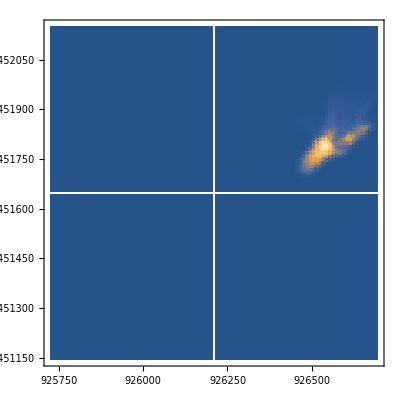

```mathematica
Show[Table[dessinPartH[i],{i,ngrid}],PlotRange->All]
```

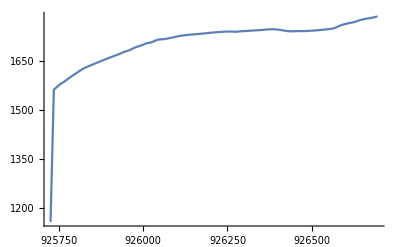

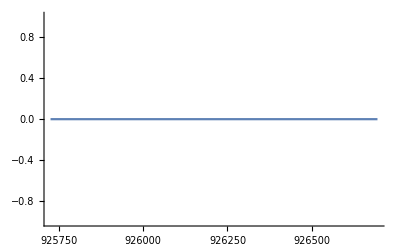

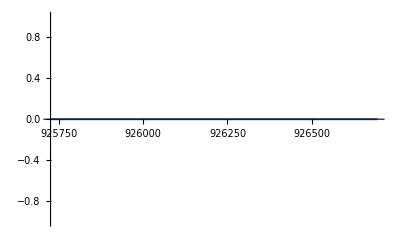

```mathematica
Plot[interEta[index][x,6451800],{x,xmin,xmax},PlotRange->All]
Plot[Sqrt[interP[index][x,6451600]/300*2],{x,xmin,xmax},PlotRange->All]
Plot[interH[index][x,6451600],{x,xmin,xmax}]
```

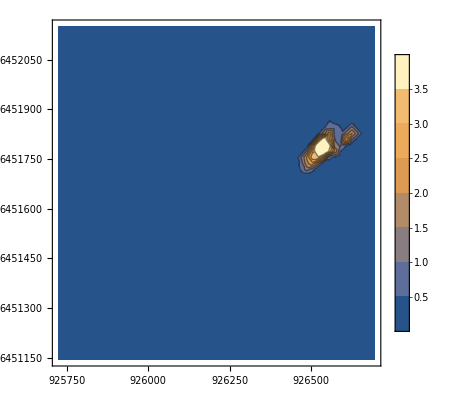

```mathematica
ContourPlot[interH[index][x,y],{x,xmin,xmax},{y,ymin,ymax},PlotLegends->Automatic]
```

## Importing and processing outputfiles

### fortq.xxxx

```mathematica
SetDirectory[ClawpackDirectory]
ndSim=Length@listeQ
nn=0;time=0;
Print["status : ",ProgressIndicator[Dynamic[nn],{0,ndSim}]," ",Dynamic[Round[nn/ndSim*100]], "% Done. Time t = ",Dynamic[time], " s"] 
fncJoin[x_,y_]:= {x,y}

ρ=300;
g=9.81;
Do[
nn=index;
colonneH={};
colonneHU={};
colonneHV={};
position={};
(* reading the time information *)
dataTimes=ReadList[listeT[[index]],"Word",RecordLists->True];
infoTimes={#[[2]],DataTransformation[#[[1]] ]}&/@Take[dataTimes,3];
ttt=infoTimes[[1,2]];
time=ttt;
dataTimes=ReadList[listeT[[index]],"Word",RecordLists->True];
(* reading the corresponding fort.q file *)
data=ReadList[listeQ[[index]],"Word",RecordLists->True];

(* determining when the AMR level 2 starts and dropping these data *)
If[
MemberQ[data,{"2","AMR_level"}],imax=Position[data,{"2","AMR_level"}][[1,1]]-2;
newdata=Take[data,imax],
newdata=data];
(* determining the position of each level 1 grid *)
indiceGrid=Flatten@Position[newdata,{_,"grid_number"}];
(* reading the (mx, my) dimensions *)
ValeursMx=ToExpression@newdata[[#+2]][[1]]&/@indiceGrid;
ValeursMy=ToExpression@newdata[[#+3]][[1]]&/@indiceGrid;
(* reading the (xll, yll) positions *)
ValeursXl=DataTransformation@newdata[[#+4]][[1]]&/@indiceGrid;
ValeursYl=DataTransformation@newdata[[#+5]][[1]]&/@indiceGrid;
(* reading the (dx, dy) mesh size *)
ValeursDx=DataTransformation@newdata[[#+6]][[1]]&/@indiceGrid;
ValeursDy=DataTransformation@newdata[[#+7]][[1]]&/@indiceGrid;
Do[
(* for each grid, extracting the columns 1 to 3 *)
col1=#[[1]]&/@Map[DataTransformation[#]&,Take[newdata,{indiceGrid[[i]]+8,indiceGrid[[i]]+ValeursMx[[i]] ValeursMy[[i]]+7}],{2}] ;
col2=#[[2]]&/@Map[DataTransformation[#]&,Take[newdata,{indiceGrid[[i]]+8,indiceGrid[[i]]+ValeursMx[[i]] ValeursMy[[i]]+7}],{2}] ;
col3=#[[3]]&/@Map[DataTransformation[#]&,Take[newdata,{indiceGrid[[i]]+8,indiceGrid[[i]]+ValeursMx[[i]] ValeursMy[[i]]+7}],{2}] ;
(* calculating the position of (xi, yi) *)
pos={ValeursXl[[i]]+(#[[1]]-0.5)ValeursDx[[i]],ValeursYl[[i]]+(#[[2]]-0.5)ValeursDy[[i]]}&/@(({#[[2]],1+#[[1]]}&/@(QuotientRemainder[#,ValeursMx[[i]]]&/@Range[ValeursMx[[i]] ValeursMy[[i]]]))/.{0,x_}->{ValeursMx[[i]],x-1});
colonneH={colonneH,col1};
colonneHU={colonneHU,col2};
colonneHV={colonneHV,col3};
position={position,pos},
{i,Length@indiceGrid}];

colonneU=Flatten@colonneHU/(ϵ+Flatten@colonneH);
colonneV=Flatten@colonneHV/(ϵ+Flatten@colonneH);
colonnePc=ρ (colonneU^2+colonneV^2)/2.;
colonnePh=ρ g Flatten@colonneH;
gridH=Partition[Flatten@MapThread[fncJoin,{Partition[Flatten@position,2],Flatten@colonneH}],3];
gridHU=Partition[Flatten@MapThread[fncJoin,{Partition[Flatten@position,2],Flatten@colonneHU}],3];
gridHV=Partition[Flatten@MapThread[fncJoin,{Partition[Flatten@position,2],Flatten@colonneHV}],3];
gridPc=Partition[Flatten@MapThread[fncJoin,{Partition[Flatten@position,2],colonnePc}],3];
gridPh=Partition[Flatten@MapThread[fncJoin,{Partition[Flatten@position,2],colonnePh}],3];
interH[index]=Interpolation[gridH,InterpolationOrder->1];
interPc[index]=Interpolation[gridPc,InterpolationOrder->1];
interPh[index]=Interpolation[gridPh,InterpolationOrder->1];
{{xmin,xmax},{ymin,ymax}}=interH[index]["Domain"]  ,
{index,1,ndSim}]//AbsoluteTiming
```

D:\qgis_val\clawpack\valdisere-1-300\_output

11

status :  % Done. Time t =  s

{1332.6,Null}

### raster.xxxx

```mathematica
SetDirectory[ClawpackDirectory]
ndSim=Length@listeR
nn=0;time=0;
Print["status : ",ProgressIndicator[Dynamic[nn],{0,ndSim}]," ",Dynamic[Round[nn/ndSim*100]], "% Done. Time t = ",Dynamic[time], " s"] 
 
dt=tmax/nsim
Do[
(* reading the time information *)
time=(index-1)dt;nn=index;
(* reading the corresponding raster file *)
data=ReadList[listeR[[index]],"Word",RecordLists->True];
colonneH=Map[Internal`StringToDouble[#]&, {#[[1]], #[[2]], #[[3]] }&/@data,{2}];
colonneV=Map[Internal`StringToDouble[#]&, {#[[1]], #[[2]], #[[6]] }&/@data,{2}];
colonnePc={#[[1]], #[[2]], ρ#[[3]]^2/2. }&/@colonneV  ;
colonnePh={#[[1]], #[[2]], ρ g#[[3]]  }&/@colonneH  ;
 
interH[index]=Interpolation[colonneH,InterpolationOrder->1];
interPc[index]=Interpolation[colonnePc,InterpolationOrder->1];
interPh[index]=Interpolation[colonnePh,InterpolationOrder->1];
{{xmin,xmax},{ymin,ymax}}=interH[index]["Domain"]  ,
{index,1,ndSim}]//AbsoluteTiming
```

D:\qgis_savinaz_20200511\clawpack\run-1-100\_output

7

status :  % Done. Time t =  s

9

{179.998,Null}

```mathematica
interPc[ndSim]["Domain"]
```

{{1.51122×10^14,1.51548×10^14},{6.33741×10^15,6.3396×10^15}}

### Plotting cross sections

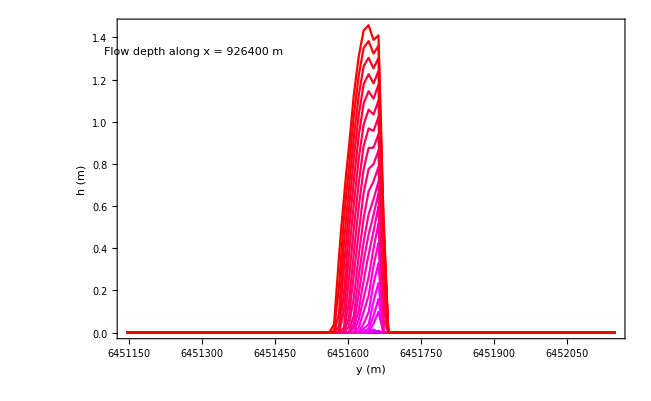

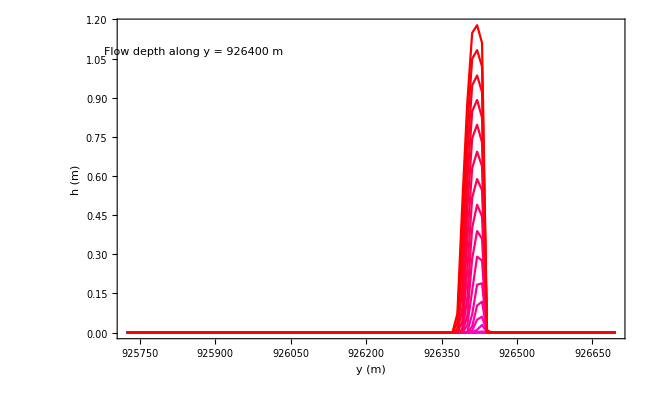

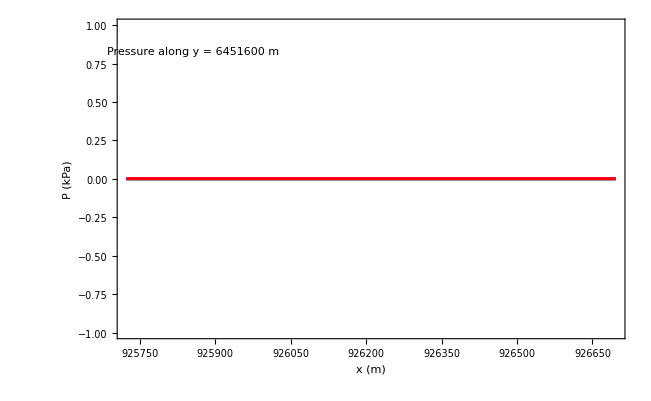

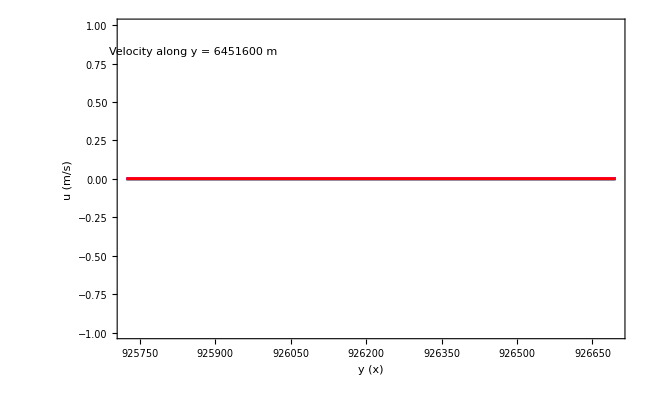

```mathematica
xtest=926400;
ytest=6451600;
Show[Table[Plot[interH[i][xtest,y],{y,ymin,ymax},PlotStyle->Hue[i/ndSim],PlotRange->All],{i,1,ndSim}],PlotRange->All,Frame->True,FrameLabel->{"y (m)","h (m)"},
Epilog->Text["Flow depth along x = "<>ToString[xtest]<> " m",Scaled[{0.15,0.9}]]] 
Show[Table[Plot[interH[i][x,ytest],{x,xmin,xmax},PlotStyle->Hue[i/ndSim],PlotRange->All],{i,1,ndSim}],Frame->True,FrameLabel->{"y (m)","h (m)"},
Epilog->Text["Flow depth along y = "<>ToString[xtest]<> " m",Scaled[{0.15,0.9}]]]
Show[Table[Plot[interP[i][x,ytest],{x,xmin,xmax},PlotStyle->Hue[i/ndSim],PlotRange->All],{i,1,ndSim}],PlotRange->All,Frame->True,FrameLabel->{"x (m)","P (kPa)"},
Epilog->Text["Pressure along y = "<>ToString[ytest]<> " m",Scaled[{0.15,0.9}]]]
Show[Table[Plot[Sqrt[interUy[i][x,ytest]^2+interUx[i][x,ytest]^2],{x,xmin,xmax},PlotStyle->Hue[i/ndSim],PlotRange->All],{i,1,ndSim}],PlotRange->All,Frame->True,FrameLabel->{"y (x)","u (m/s)"},
Epilog->Text["Velocity along y = "<>ToString[ytest]<> " m",Scaled[{0.15,0.9}]]]
```

```mathematica
maxp=Table[{3(i-1),Max@Table[interP[i][x,y],{x,xmin,xmax,5},{y,ymin,ymax,5}]},{i,ndSim}]
maxh=Table[{3(i-1),Max@Table[interH[i][x,y],{x,xmin,xmax,5},{y,ymin,ymax,5}]},{i,ndSim}]
```

{{0,0.},{3,0.},{6,0.},{9,0.},{12,0.},{15,0.},{18,0.},{21,0.},{24,0.},{27,0.},{30,0.},{33,0.},{36,0.},{39,0.},{42,0.},{45,0.},{48,0.},{51,0.},{54,0.},{57,0.},{60,0.},{63,0.},{66,0.},{69,0.},{72,0.},{75,0.},{78,0.},{81,0.},{84,0.},{87,0.},{90,0.},{93,0.},{96,0.},{99,0.},{102,0.},{105,0.},{108,0.},{111,0.},{114,0.},{117,0.},{120,0.},{123,0.},{126,0.},{129,0.},{132,0.},{135,0.},{138,0.},{141,0.},{144,0.},{147,0.},{150,0.},{153,0.},{156,0.},{159,0.},{162,0.},{165,0.},{168,0.},{171,0.},{174,0.},{177,0.},{180,0.},{183,0.},{186,0.},{189,0.},{192,0.},{195,0.},{198,0.},{201,0.},{204,0.},{207,0.},{210,0.},{213,0.},{216,0.},{219,0.},{222,0.},{225,0.},{228,0.},{231,0.},{234,0.},{237,0.},{240,0.},{243,0.},{246,0.},{249,0.},{252,0.},{255,0.},{258,0.},{261,0.},{264,0.},{267,0.},{270,0.},{273,0.},{276,0.},{279,0.},{282,0.},{285,0.},{288,0.},{291,0.},{294,0.},{297,0.},{300,0.}}

{{0,2.},{3,2.74868},{6,3.20416},{9,3.44374},{12,3.59186},{15,3.73093},{18,3.85956},{21,3.96681},{24,4.22263},{27,4.48499},{30,4.65915},{33,4.82944},{36,4.94989},{39,5.02011},{42,5.04152},{45,5.09628},{48,5.132},{51,5.13486},{54,5.11475},{57,5.07572},{60,5.00686},{63,4.98386},{66,5.10286},{69,5.17918},{72,5.27033},{75,5.33223},{78,5.37632},{81,5.41294},{84,5.44576},{87,5.49018},{90,5.54714},{93,5.60382},{96,5.64659},{99,5.70093},{102,5.7368},{105,5.76377},{108,5.79261},{111,5.81123},{114,5.8227},{117,5.83027},{120,5.83464},{123,5.83375},{126,5.82956},{129,5.8214},{132,5.80998},{135,5.79584},{138,5.777},{141,5.75619},{144,5.73264},{147,5.70367},{150,5.67653},{153,5.65776},{156,5.63465},{159,5.61832},{162,5.60398},{165,5.58583},{168,5.56625},{171,5.53385},{174,5.49812},{177,5.45875},{180,5.41569},{183,5.36899},{186,5.32075},{189,5.28137},{192,5.23785},{195,5.19378},{198,5.14788},{201,5.07747},{204,5.00756},{207,4.93365},{210,4.87996},{213,4.82467},{216,4.76775},{219,4.70904},{222,4.64934},{225,4.59314},{228,4.50979},{231,4.42965},{234,4.34782},{237,4.26236},{240,4.17614},{243,4.088},{246,4.00014},{249,3.91351},{252,3.82703},{255,3.74784},{258,3.67766},{261,3.61045},{264,3.53909},{267,3.47473},{270,3.41827},{273,3.36452},{276,3.30783},{279,3.25026},{282,3.19137},{285,3.1323},{288,3.07326},{291,3.0529},{294,3.10298},{297,3.15332},{300,3.19894}}

```mathematica
Mean@Flatten[Table[interP[10][x,y],{x,xmin,xmax,5},{y,ymin,ymax,5}],1]
```

0.

```mathematica
meanp=Table[{3(i-1),Mean@Flatten[Table[interP[i][x,y],{x,xmin,xmax,5},{y,ymin,ymax,5}],1]},{i,ndSim}];
```

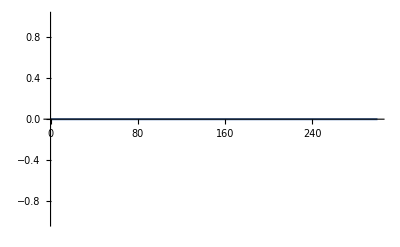

```mathematica
ListPlot[{#[[1]],Sqrt[#[[2]]/ 300*2*1000]}&/@meanp,Joined->True,PlotRange->All]
```

-Graphics-

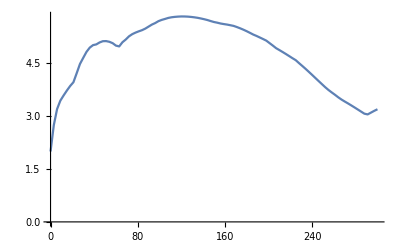

```mathematica
ListPlot[{#[[1]],Sqrt[#[[2]]/ 300*2*1000]}&/@maxp,Joined->True,PlotRange->All]
ListPlot[maxh,Joined->True,PlotRange->All]
```

### Overlaying map on topo

1

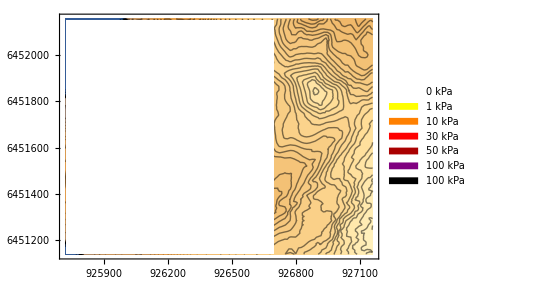

```mathematica
ii=1
 Show[vue,DensityPlot[interP[ii][x,y],{x,xmin,xmax},{y,ymin,ymax}, PlotPoints->50,   PlotRange->All, PlotLegends->SwatchLegend[{White,Yellow,Orange,Red,Darker@Red,Purple,Black},{"0 kPa","1 kPa","10 kPa"," 30 kPa"," 50 kPa"," 100 kPa"," 100 kPa"}],
 ColorFunction -> (Blend[{
{0,{White,Opacity[0]}},
{0.1, White}, 
{1, Yellow}, 
{10, Orange}, 
{30, Red},
{50, Darker[Red]},
{100, Purple},
{1000, Black}},
 #] &),ColorFunctionScaling->False,
Epilog->Text[Style["kinetic pressure at time t = "<>ToString[(ii-1)*2 ]<>" s",16],Scaled[{0.05,0.9}],{-1,0},{1,0}],ImageSize->Large] ]
```

### Exporting Animation

```mathematica
liste= Table[Show[vue,
DensityPlot[
interH[i][x,y],{x,xmin,xmax},{y,ymin,ymax},
 PlotPoints->100, PlotRange->All,
 ColorFunction -> (Blend[{
{0,{White,Opacity[0]}}, 
{0.1, Yellow}, 
{0.5, Orange}, 
{1, Red},
{1.5, Darker[Red]},
{2, Purple},
{10, Black}},
 #] &),ColorFunctionScaling->False 
]  ,Epilog->Text[Style["t = "<>ToString[(i-1)*2 ]<>" s",16],Scaled[{0.15,0.9}]],ImageSize->Large],
{i,ndSim}] ;
Export["animationH.avi",liste,"FrameRate"->2,ImageResolution->100]
```

animationH.avi

```mathematica
liste= Table[ Show[vue,
DensityPlot[
interP[i][x,y],{x,xmin,xmax},{y,ymin,ymax},
 PlotPoints->50, PlotRange->All,
 ColorFunction -> (Blend[{
{0,{White,Opacity[0]}},
{0.01, White}, 
{10, Orange}, 
{30, Red},
{50, Darker[Red]},
{100, Purple},
{1000, Black}},
 #] &),ColorFunctionScaling->False,
Epilog->Text[Style["t = "<>ToString[(i-1)*2 ]<>" s",16],Scaled[{0.15,0.9}]],ImageSize->Large] ],
{i,ndSim}] ;
Export["animationPwithB.avi",liste,"FrameRate"->2,ImageResolution->100]
```

animationPwithB.avi

```mathematica
liste= Table[
ContourPlot[
interP[i][x,y],{x,xmin,xmax},{y,ymin,ymax},
 PlotPoints->50, Contours->5,PlotRange->All,
 ColorFunction -> (Blend[{
{0, White}, 
{1, Yellow}, 
{10, Orange}, 
{30, Red},
{50, Darker[Red]},
{100, Purple},
{1000, Black}},
 #] &),ColorFunctionScaling->False,
Epilog->Text[Style["t = "<>ToString[(i-1)*2 ]<>" s",16],Scaled[{0.15,0.9}]],ImageSize->Large] ,
{i,31}] ;
Export["animationPc.avi",liste,"FrameRate"->2,ImageResolution->100]
```

animationPc.avi

## Gauges

```mathematica
listeG=FileNames["gauge*.txt"] 
nbGauge=Length@listeG
```

{gauge00001.txt,gauge00002.txt,gauge00003.txt,gauge00004.txt,gauge00005.txt,gauge00006.txt,gauge00007.txt,gauge00008.txt,gauge00009.txt,gauge00010.txt}

10

```mathematica
Do[
dataGRaw=StringSplit[#]&/@Drop[Import[listeG[[i]],"Data"],2] ;
dataGaugeH[i]={ToExpression@StringReplace[#[[1,2]], "E"-> "*10^"],ToExpression@StringReplace[#[[1,3]], "E"-> "*10^"]}&/@dataGRaw;
dataGaugeQ[i]={ToExpression@StringReplace[#[[1,2]], "E"-> "*10^"],ToExpression@StringReplace[#[[1,4]], "E"-> "*10^"]}&/@dataGRaw,
{i,nbGauge}]
```

```mathematica
ListPlot@dataGaugeQ[2]
```

-Graphics-

## Export

```mathematica
index=100
```

100

```mathematica
pas=5;
{nnx,nny}=Floor[{ -xmin+xmax,-ymin+ymax}/pas]-{1,1}
fileExport=OpenWrite["RasterAvalanchePas1.asc",FormatType->OutputForm,PageWidth->Infinity];
Write[fileExport,"ncols        ",nnx];
Write[fileExport,"nrows        ",nny];
Write[fileExport,"xllcorner    ",Ceiling[xmin]];
Write[fileExport,"yllcorner    ",Ceiling[ymin]];
Write[fileExport,"cellsize     ",pas];
Write[fileExport,"nodata_value ",0];
Do[
Write[fileExport,TableForm[Table[Round[interP[index][ xmin+(j-1/2)*pas ,ymin+(i-1/2)*pas ]*100]/100. , {j,nnx} ],TableDirections->Row]],
{i,  nny ,1,-1}]
Close[fileExport]
```

{193,199}

RasterAvalanchePas1.asc